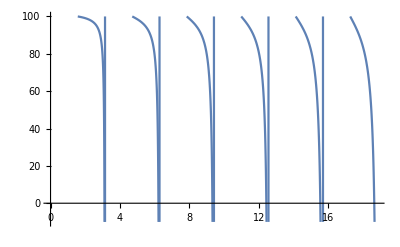

{k→3.138454209684535}

{k→6.27690848113237}

{k→9.41536287609952}

{k→12.55381745632742}

{k→15.69227228353565}

{k→18.83072741941467}

{k→21.96918292561855}

{k→25.10763886375769}

{k→28.2460952953916}

```mathematica
Clear[KL]
Plot[KL+ k Cot[k]/. KL -> 100., {k,0,6π}, PlotRange -> {-10, 100}]
For[n=1,n<10,n++,Print[NumberForm[FindRoot[KL+k Cot[k]/. KL -> 1000., {k, n*π*.9999}], 20]]]
```

```mathematica
3.138454209684535^2
6.27690848113237^2
9.41536287609952^2
28.2460952953916^2
```

9.84989

39.3996

88.6491

797.842